```mathematica
f[x_]:=x^2
range={-7,7,.1};
```

```mathematica
Round[InverseFourier[Fourier[f/@(Range@@range)]], 0.001]
```

{49.,47.61,46.24,44.89,43.56,42.25,40.96,39.69,38.44,37.21,36.,34.81,33.64,32.49,31.36,30.25,29.16,28.09,27.04,26.01,25.,24.01,23.04,22.09,21.16,20.25,19.36,18.49,17.64,16.81,16.,15.21,14.44,13.69,12.96,12.25,11.56,10.89,10.24,9.61,9.,8.41,7.84,7.29,6.76,6.25,5.76,5.29,4.84,4.41,4.,3.61,3.24,2.89,2.56,2.25,1.96,1.69,1.44,1.21,1.,0.81,0.64,0.49,0.36,0.25,0.16,0.09,0.04,0.01,0.,0.01,0.04,0.09,0.16,0.25,0.36,0.49,0.64,0.81,1.,1.21,1.44,1.69,1.96,2.25,2.56,2.89,3.24,3.61,4.,4.41,4.84,5.29,5.76,6.25,6.76,7.29,7.84,8.41,9.,9.61,10.24,10.89,11.56,12.25,12.96,13.69,14.44,15.21,16.,16.81,17.64,18.49,19.36,20.25,21.16,22.09,23.04,24.01,25.,26.01,27.04,28.09,29.16,30.25,31.36,32.49,33.64,34.81,36.,37.21,38.44,39.69,40.96,42.25,43.56,44.89,46.24,47.61,49.}

```mathematica
f/@(Range@@range)
```

{49.,47.61,46.24,44.89,43.56,42.25,40.96,39.69,38.44,37.21,36.,34.81,33.64,32.49,31.36,30.25,29.16,28.09,27.04,26.01,25.,24.01,23.04,22.09,21.16,20.25,19.36,18.49,17.64,16.81,16.,15.21,14.44,13.69,12.96,12.25,11.56,10.89,10.24,9.61,9.,8.41,7.84,7.29,6.76,6.25,5.76,5.29,4.84,4.41,4.,3.61,3.24,2.89,2.56,2.25,1.96,1.69,1.44,1.21,1.,0.81,0.64,0.49,0.36,0.25,0.16,0.09,0.04,0.01,0.,0.01,0.04,0.09,0.16,0.25,0.36,0.49,0.64,0.81,1.,1.21,1.44,1.69,1.96,2.25,2.56,2.89,3.24,3.61,4.,4.41,4.84,5.29,5.76,6.25,6.76,7.29,7.84,8.41,9.,9.61,10.24,10.89,11.56,12.25,12.96,13.69,14.44,15.21,16.,16.81,17.64,18.49,19.36,20.25,21.16,22.09,23.04,24.01,25.,26.01,27.04,28.09,29.16,30.25,31.36,32.49,33.64,34.81,36.,37.21,38.44,39.69,40.96,42.25,43.56,44.89,46.24,47.61,49.}

```mathematica
nums=Join[#,Reverse[Conjugate/@Rest[#]]]&[RandomComplex[{0, 1+I}, {20}]/.({a_, b___}->Prepend[{b}, Re[a]])]
```

{0.58367,0.765179+0.301007 ⅈ,0.170567+0.669776 ⅈ,0.643609+0.714517 ⅈ,0.955709+0.635194 ⅈ,0.444054+0.906065 ⅈ,0.136196+0.131305 ⅈ,0.745571+0.311296 ⅈ,0.568888+0.303683 ⅈ,0.175897+0.430931 ⅈ,0.660328+0.348331 ⅈ,0.593753+0.330023 ⅈ,0.98134+0.449058 ⅈ,0.896631+0.361263 ⅈ,0.372348+0.338917 ⅈ,0.589131+0.936604 ⅈ,0.000707148+0.751836 ⅈ,0.642239+0.702611 ⅈ,0.535129+0.0545066 ⅈ,0.99067+0.735731 ⅈ,0.99067-0.735731 ⅈ,0.535129-0.0545066 ⅈ,0.642239-0.702611 ⅈ,0.000707148-0.751836 ⅈ,0.589131-0.936604 ⅈ,0.372348-0.338917 ⅈ,0.896631-0.361263 ⅈ,0.98134-0.449058 ⅈ,0.593753-0.330023 ⅈ,0.660328-0.348331 ⅈ,0.175897-0.430931 ⅈ,0.568888-0.303683 ⅈ,0.745571-0.311296 ⅈ,0.136196-0.131305 ⅈ,0.444054-0.906065 ⅈ,0.955709-0.635194 ⅈ,0.643609-0.714517 ⅈ,0.170567-0.669776 ⅈ,0.765179-0.301007 ⅈ}

```mathematica
Round[InverseFourier[nums], 0.01]
```

{3.57,1.76,-0.01,1.3,0.3,-0.2,0.41,-0.38,-0.04,0.21,0.58,0.68,-0.18,-0.12,-0.65,-0.23,0.13,-0.05,-0.14,0.33,-0.7,0.17,-0.89,0.51,-0.09,-0.06,-0.23,0.4,0.06,0.41,0.25,-0.13,0.14,0.34,-0.99,0.12,-1.05,0.07,-1.94}

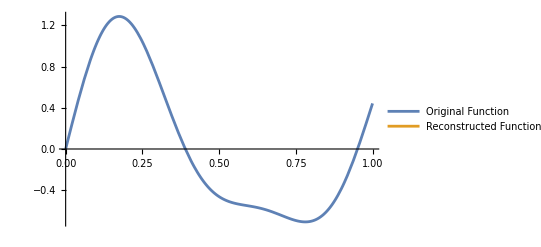

```mathematica
(*Define the original function f*)
f[x_]:=Sin[7x] + 0.4Sin[12x]

(*Sampling the function*)
range={0,1};
delta=0.01;
points=Table[f[x],{x,range[[1]],range[[2]],delta}];

(*Compute the Fourier coefficients*)
Na=Length[points];
fourierCoeffs=Fourier[points];

(*Reconstruct the function from Fourier coefficients*)
reconstructF[x_]:=Sum[(fourierCoeffs[[n+1]]*Exp[2 Pi I n x/(range[[2]]-range[[1]])])/Na,{n,0,Na-1}]

(*Plot the original and reconstructed function*)
Plot[{f[x],reconstructF[x]},{x,range[[1]],range[[2]]},PlotLegends->{"Original Function","Reconstructed Function"}]
```

```mathematica
(*Define the original function f*)
f[x_]:=Sin[2 Pi x]+0.5 Sin[4 Pi x]

(*Sampling the function*)
range={0,1};
delta=0.01;
points=Table[f[x],{x,range[[1]],range[[2]],delta}];

(*Compute the Fourier coefficients*)
numPoints=Length[points];  (*Use numPoints instead of N*)
fourierCoeffs=Fourier[points];

(*Reconstruct the function from Fourier coefficients*)
reconstructF[x_]:=Sum[(fourierCoeffs[[n+1]]*Exp[2 Pi I n x/(range[[2]-range[[1]]])])/numPoints,{n,0,numPoints-1}]

(*Plot the original and reconstructed function*)
Plot[{f[x],reconstructF[x]},{x,range[[1]],range[[2]]},PlotLegends->{"Original Function","Reconstructed Function"}]
```

Syntax::sntxb: Expression cannot begin with "[2]-range[[1]]".

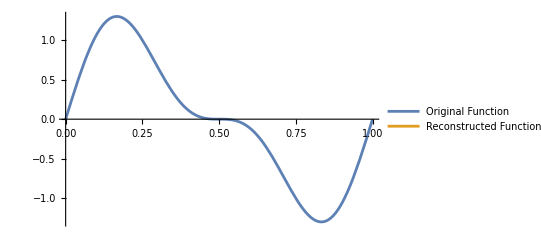

```mathematica
(*Define the original function f*)f[x_]:=Sin[2 Pi x]+0.5 Sin[4 Pi x]

(*Sampling the function*)
range={0,1};
delta=0.01;
points=Table[f[x],{x,range[[1]],range[[2]],delta}];

(*Compute the Fourier coefficients*)
numPoints=Length[points];
fourierCoeffs=Fourier[points];

(*Reconstruct the function from Fourier coefficients*)
reconstructF[x_]:=Sum[(fourierCoeffs[[n+1]]*Exp[2 Pi I n x/(range[[2]]-range[[1]])])/numPoints,{n,0,numPoints-1}]

(*Plot the original and reconstructed function*)
Plot[{f[x],reconstructF[x]},{x,range[[1]],range[[2]]},PlotLegends->{"Original Function","Reconstructed Function"}]
```

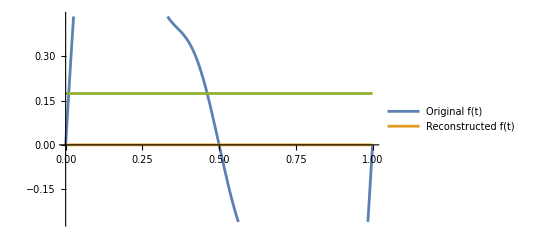

```mathematica
(*Define the function f,which is a summation of sine curves*)f[t_]:=Sin[2 Pi t]+0.5 Sin[4 Pi t]+0.25 Sin[6 Pi t];  (*Example function*)

(*Specify the range of points to evaluate*)
range={0,1};  (*Define the interval over which f is defined*)
numPoints=100; (*Number of points for Fourier transformation*)

(*Evaluate the function at these points*)
points=f/@(Range@@range/(numPoints-1));

(*Compute the Fourier Transform (or coefficients) of the points*)
fourierCoefficients=Fourier[points];

(*Now reconstruct the function using the inverse Fourier Transform*)
(*Create a time variable for reconstruction*)
tValues=Range[0,1,1/(numPoints-1)];

(*Use the Inverse Fourier Transform to get the reconstructed function*)
reconstructedFunction=InverseFourier[fourierCoefficients];

(*Plot the original function and the reconstructed function*)
Plot[{f[t],reconstructedFunction},{t,0,1},PlotLegends->{"Original f(t)","Reconstructed f(t)"}]
```

Set::wrsym: Symbol N is Protected.

Part::pkspec1: The expression 1+k cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NSum::nslim: Limit of summation N is not a number.

General::stop: Further output of NSum::nslim will be suppressed during this calculation.

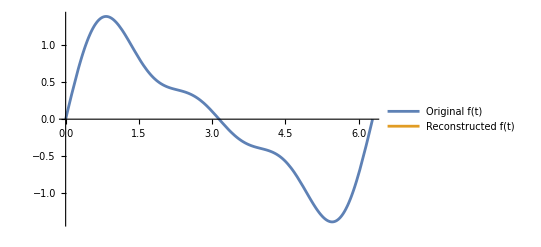

```mathematica
(*Step 1:Define the original function f(t) as a summation of sine curves*)T=2 Pi; (*Define the period*)
f[t_]:=Sin[t]+0.5 Sin[2 t]+0.25 Sin[3 t];  (*Example function*)

(*Step 2:Sample points from f(t) over a specified range*)
range={0,2 Pi}; (*Define the range for t*)
points=f/@(Range@@range);  (*Sample points from f(t)*)

(*Step 3:Compute the Fourier coefficients using the Fourier transform*)
N=Length[points];  (*Number of sampled points*)
fourierCoeffs=Fourier[points];  (*Compute the DFT*)

(*Step 4:Reconstruct the function using the Inverse Fourier Transform*)
reconstructedFunc[t_]:=Sum[1/N*fourierCoeffs[[k+1]]*Exp[I (2 Pi (k-1) t)/T],{k,1,N}];

(*Plot the original and reconstructed function*)
Plot[{f[t],Re[reconstructedFunc[t]]},{t,0,2 Pi},PlotLegends->{"Original f(t)","Reconstructed f(t)"},PlotRange->All]
```

Part::partw: Part 11 of {0.+0. ⅈ,0.480088+1.47756 ⅈ,0.272989+0.375737 ⅈ,-0.100267-0.0728482 ⅈ,-0.460459-0.149612 ⅈ,-0.384701+0. ⅈ,-0.460459+0.149612 ⅈ,-0.100267+0.0728482 ⅈ,0.272989-0.375737 ⅈ,0.480088-1.47756 ⅈ} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

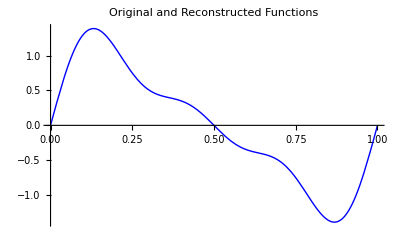

```mathematica
(*Define the function f(x)*)f[x_]:=Sin[2*Pi*x]+0.5*Sin[4*Pi*x]+0.25*Sin[6*Pi*x]

(*Sample points from f over a specific range*)
range={0,1};  (*Define the range for sampling*)
Na=10;          (*Number of samples*)
points=Table[f[x],{x,range[[1]],range[[2]],(range[[2]]-range[[1]])/(Na-1)}];

(*Compute the Fourier Transform to get the coefficients*)
coefficients=Fourier[points];

(*Reconstruct the function f(x) using the Fourier coefficients*)
reconstructedF[x_]:=Sum[coefficients[[k+1]] Exp[2*Pi*I*(k-1)*(x/(range[[2]]-range[[1]]))],{k,1,Na}]

(*Plot the original and reconstructed functions*)
Show[Plot[f[x],{x,range[[1]],range[[2]]},PlotStyle->Directive[Blue,Thick],PlotLabel->"Original and Reconstructed Functions"],Plot[reconstructedF[x],{x,range[[1]],range[[2]]},PlotStyle->Directive[Red,Thick]]]
```

InverseFourier::nonopt: Options expected (instead of 0.0000204286) beyond position 2 in InverseFourier[{0.+0. ⅈ,0.38838+1.95252 ⅈ,0.286087+0.690676 ⅈ,-0.159218-0.238287 ⅈ,-0.125067-0.125067 ⅈ,-0.11529-0.0770345 ⅈ,«4»,-0.111167+0.046047 ⅈ,-0.11529+0.0770345 ⅈ,-0.125067+0.125067 ⅈ,-0.159218+0.238287 ⅈ,0.286087-0.690676 ⅈ,0.38838-1.95252 ⅈ},«1»,«24»]. An option must be a rule or a list of rules.

InverseFourier::nonopt: Options expected (instead of 0.0204286) beyond position 2 in InverseFourier[{0.+0. ⅈ,0.38838+1.95252 ⅈ,0.286087+0.690676 ⅈ,-0.159218-0.238287 ⅈ,-0.125067-0.125067 ⅈ,-0.11529-0.0770345 ⅈ,«4»,-0.111167+0.046047 ⅈ,-0.11529+0.0770345 ⅈ,-0.125067+0.125067 ⅈ,-0.159218+0.238287 ⅈ,0.286087-0.690676 ⅈ,0.38838-1.95252 ⅈ},«1»,0.0204286]. An option must be a rule or a list of rules.

General::stop: Further output of InverseFourier::nonopt will be suppressed during this calculation.

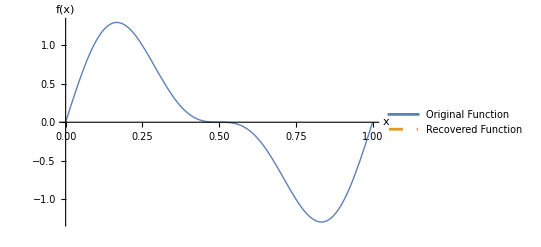

```mathematica
(*Step 1:Define the original function*)f[x_]:=Sin[2*Pi*x]+0.5*Sin[4*Pi*x]  (*Example function*)

(*Step 2:Sample the function at specific points*)
range={0,1};  (*Define the range for sampling*)
numPoints=16;  (*Number of points to sample*)
samples=Table[f[x],{x,range[[1]],range[[2]],(range[[2]]-range[[1]])/(numPoints-1)}];

(*Step 3:Compute the Fourier Transform of the samples*)
fourierCoeffs=Fourier[samples];

(*Step 4:Recover the original function using Inverse Fourier Transform*)
recoveredFunction=InverseFourier[fourierCoeffs];

(*Create a continuous function for plotting*)
continuousFunc[x_]:=Re[InverseFourier[fourierCoeffs,FourierParameters->{1,-1},x]];

(*Step 5:Plot the original and recovered functions*)
Plot[{f[x],continuousFunc[x]},{x,range[[1]],range[[2]]},PlotLegends->{"Original Function","Recovered Function"},PlotStyle->{Thick,Dashed},AxesLabel->{"x","f(x)"}]
```

```mathematica
(*Step 1:Define the original function*)f[x_]:=Sin[2*Pi*x]+0.5*Sin[4*Pi*x]  (*Example function*)

(*Step 2:Sample the function at specific points*)
range={0,1};  (*Define the range for sampling*)
numPoints=16;  (*Number of points to sample*)
samples=Table[f[x],{x,range[[1]],range[[2]],(range[[2]]-range[[1]])/(numPoints-1)}];

(*Step 3:Compute the Fourier Transform of the samples*)
fourierCoeffs=Fourier[samples];

(*Step 4:Recover the original function using Inverse Fourier Transform*)
recoveredSamples=InverseFourier[fourierCoeffs];

(*Create a continuous function for plotting using interpolation*)
continuousFunc[x_]:=Interpolation[Table[{x[[i]],recoveredSamples[[i]]},{i,Length[recoveredSamples]}]]

(*Step 5:Plot the original and recovered functions*)
Plot[{f[x],continuousFunc[x]},{x,range[[1]],range[[2]]},PlotLegends->{"Original Function","Recovered Function"},PlotStyle->{Thick,Dashed},AxesLabel->{"x","f(x)"}]
```

Part::partd: Part specification 0.0000204286⟦1⟧ is longer than depth of object.

Part::partd: Part specification 0.0000204286⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0.0000204286⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Interpolation::indat: Data point {0.0000204286⟦1⟧,0.+0. ⅈ} contains abscissa 0.0000204286⟦1⟧, which is not a real number.

Interpolation::indat: Data point {0.0204286⟦1⟧,0.+0. ⅈ} contains abscissa 0.0204286⟦1⟧, which is not a real number.

Interpolation::indat: Data point {0.0408368⟦1⟧,0.+0. ⅈ} contains abscissa 0.0408368⟦1⟧, which is not a real number.

General::stop: Further output of Interpolation::indat will be suppressed during this calculation.

-Graphics-

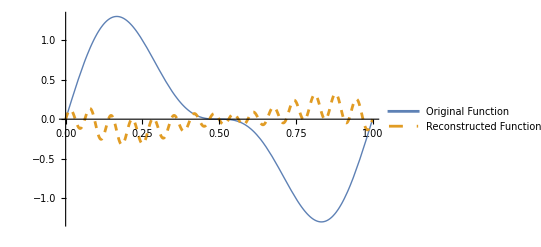

```mathematica
(*Step 1:Define the original function*)
f[x_]:=Sin[2*Pi*x]+0.5*Sin[4*Pi*x]  (*Example function*)

(*Step 2:Sample the function at specific points*)
range={0,1};  (*Define the range for sampling*)
numPoints=16;  (*Number of points to sample*)
samples=Table[f[x],{x,range[[1]],range[[2]],(range[[2]]-range[[1]])/(numPoints-1)}];

(*Step 3:Compute the Fourier Transform of the samples*)
fourierCoeffs=Fourier[samples];

(*Step 4:Define the reconstruction function*)reconstruct[t_]:=Re@Sum[fourierCoeffs[[k]]*Exp[I*2*Pi*(k-1)*t/(range[[2]]-range[[1]])],{k,1,Length[fourierCoeffs]}]/Length[fourierCoeffs];

(*Step 5:Plot original and reconstructed functions*)
Plot[{f[x],reconstruct[x]},{x,range[[1]],range[[2]]},PlotLegends->{"Original Function","Reconstructed Function"},PlotStyle->{Thick,Dashed}]
```

```mathematica
reconstruct[.5]
```

-0.00113584+8.32667×10^-17 ⅈ

```mathematica
(*Step 1:Define the original function*)f[x_]:=Sin[2*Pi*x]+0.5*Sin[4*Pi*x]  (*Example function*)

(*Step 2:Sample the function at specific points*)
range={0,1};  (*Define the range for sampling*)
numPoints=16;  (*Number of points to sample*)
samples=Table[f[x],{x,range[[1]],range[[2]],(range[[2]]-range[[1]])/(numPoints-1)}];

(*Step 3:Compute the Fourier Transform of the samples*)
fourierCoeffs=Fourier[samples];

(*Step 4:Define the reconstruction function,taking the real part*)
reconstruct[t_]:=Re[Sum[fourierCoeffs[[k]]*Exp[I*2*Pi*(k-1)*t/(range[[2]]-range[[1]])],{k,1,Length[fourierCoeffs]}]/Length[fourierCoeffs]];

(*Step 5:Plot original and reconstructed functions*)
Plot[{f[x],reconstruct[x]},{x,range[[1]],range[[2]]},PlotLegends->{"Original Function","Reconstructed Function"},PlotStyle->{Thick,Dashed}]
```

-Graphics-